```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../../runs/Trials/N9K9/21385198-1.dat"];
```

```mathematica
data2 = Import["../../../runs/Trials/N9K9/15650383-1.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
cmatdata = cMatOne/@data;
```

```mathematica
cmatdata2 = cMatOne/@data2;
```

```mathematica
eig = Flatten[Map[Eigenvalues, cmatdata[[All, 2;;]], {2}]];
```

```mathematica
eig2 = Flatten[Map[Eigenvalues, cmatdata2[[All, 2;;]], {2}]];
```

```mathematica
randmat = Partition[(# - 1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[σ/(√($N)), $N], Length[data]*$K], $K];
```

```mathematica
randeig = Flatten[Map[Eigenvalues, randmat, {2}]];
```

```mathematica
trX1X2 = Tr[#[[1]].#[[2]]]&/@cmatdata[[All, 2;;]]//Chop;
```

```mathematica
trX1X22 = Tr[#[[1]].#[[2]]]&/@cmatdata2[[All, 2;;]]//Chop;
```

```mathematica
trX1X2rand = Tr[#[[1]].#[[2]]]&/@randmat//Chop;
```

```mathematica
x112Re = Re[#[[1, 1, 2]]]&/@cmatdata[[All, 2;;]]//Chop;
```

```mathematica
x112Re2 = Re[#[[1, 1, 2]]]&/@cmatdata2[[All, 2;;]]//Chop;
```

```mathematica
x112Rerand= Re[#[[1, 1, 2]]]&/@randmat//Chop;
```

```mathematica
x433 = Re[#[[4, 3, 3]]]&/@cmatdata[[All, 2;;]]//Chop;
x4332 = Re[#[[4, 3, 3]]]&/@cmatdata2[[All, 2;;]]//Chop;
x433rand= Re[#[[4, 3, 3]]]&/@randmat//Chop;
```

```mathematica
trX1sq = Tr[#[[1]].#[[1]]]&/@cmatdata[[All, 2;;]]//Chop;
trX1sq2 = Tr[#[[1]].#[[1]]]&/@cmatdata2[[All, 2;;]]//Chop;
trX1sqrand = Tr[#[[1]].#[[1]]]&/@randmat//Chop;
```

```mathematica
trXsq = Sum[Tr[#[[α]].#[[α]]]&/@cmatdata[[All, 2;;]]//Chop, {α, 1, $K}];
trXsq2 = Sum[Tr[#[[α]].#[[α]]]&/@cmatdata2[[All, 2;;]]//Chop, {α, 1, $K}];
trXsqrand = Sum[Tr[#[[α]].#[[α]]]&/@randmat//Chop, {α, 1, $K}];
```

```mathematica
σ =StandardDeviation[x112Re]/StandardDeviation[x112Rerand]
```

0.194016

```mathematica
StandardDeviation[x112Re]/StandardDeviation[x112Rerand]
```

1.00553

```mathematica
(StandardDeviation[trX1X2]/StandardDeviation[trX1X2rand])^(1/2)
```

1.06388

```mathematica
StandardDeviation[eig]/StandardDeviation[randeig]
```

0.964559

```mathematica
(StandardDeviation[trX1sq]/StandardDeviation[trX1sqrand])^(1/2)
```

1.04099

```mathematica
(StandardDeviation[trXsq]/StandardDeviation[trXsqrand])^(1/2)
```

0.777207

```mathematica
(StandardDeviation[x433]/StandardDeviation[x433rand])
```

0.984681

```mathematica
(Mean[trX1sq]/Mean[trX1sqrand])^(1/2)
```

0.963957

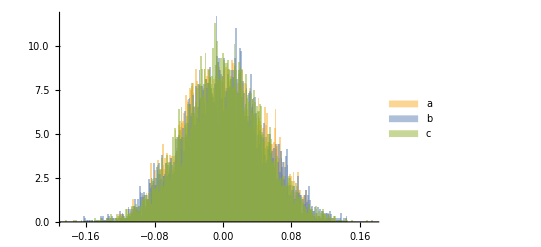

```mathematica
Histogram[{x112Re, x112Re2, x112Rerand}, 450, PDF, ChartLegends->{"a", "b", "c"}]
```

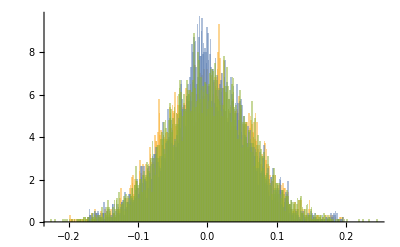

```mathematica
Histogram[{x433, x4332, x433rand}, 450, PDF]
```

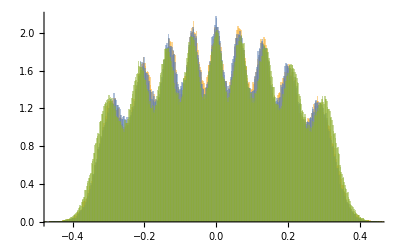

```mathematica
Histogram[{eig, eig2, randeig}, 450, PDF]
```

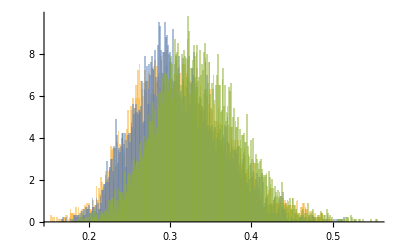

```mathematica
Histogram[{trX1sq, trX1sq2, trX1sqrand}, 450, PDF]
```

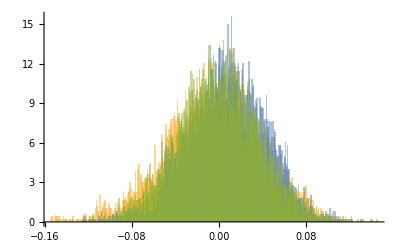

```mathematica
Histogram[{trX1X2, trX1X22, trX1X2rand}, 450, PDF
]
```

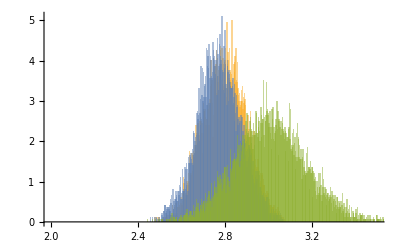

```mathematica
Histogram[{trXsq, trXsq2, trXsqrand}, 450, PDF,
PlotRange->{{2.0, 3.5}, Automatic}
]
```

```mathematica
Skewness[trXsq]
```

-0.0453794

```mathematica
Skewness[trXsq2]
```

0.00832053

```mathematica
Skewness[trXsqrand]
```

0.127634

```mathematica
Kurtosis[trXsq]
```

16.808

```mathematica
Kurtosis[trXsqrand]
```

2.99759

```mathematica
CentralMoment[trXsq, 2]
```

0.0187114

```mathematica
CentralMoment[trXsqrand, 2]
```

0.0209416

```mathematica
CentralMoment[trXsq, 3]
```

-0.00465624

```mathematica
CentralMoment[trXsqrand, 3]
```

0.00031046

```mathematica
CentralMoment[trXsq, 4]
```

0.00588474

```mathematica
CentralMoment[trXsqrand, 4]
```

0.00131459